# Introduction to Patterns

Math 213 - Math with Mathematica
Christopher Hanusa

## Overview

In this tutorial, we explore how Mathematica uses patterns.  By the end of this tutorial, you should be able to use Mathematica to check for patterns in data and lists and define function that are only valid on certain inputs.

## How Mathematica looks for patterns

In various situations, you will probably want Mathematica to determine if it sees a pattern in a list.  We'll focus solely on numbers and lists for now, but Mathematica can handle more than lists and you can read more in its tutorial "Introduction to patterns" if you need this at some point.

First, we'll introduce the function MatchQ.  Notice the Q suffix; you know that this is a function that will either output True or False.  So what does it do?

```mathematica
?MatchQ
```

That wasn't too helpful, now was it?  Here's an example from the documentation center.

```mathematica
Head[Pi]
Head[{1,2,3}]
Head[1+q]
```

Symbol

List

Plus

```mathematica
MatchQ[12345,_Integer]
MatchQ[12.345,_Integer]
```

Now you can start to guess what it is doing---it checks to see if the given input is an integer.
Mathematica will check for all sorts of objects, not just integers.
For numbers, Mathematica will check Integer, Rational, Real, and Complex.  For more examples, in the documentation center, you can go to tutorial/TypesOfNumbers.

### Underscoring patterns

Now let's talk about that underscore (_) that is before the Integer in the MatchQ function call above.  There are three types of wild cards, _, __, and ___.  That is, a single underscore, a double underscore, and a triple underscore, and they each mean something slightly different.

A single underscore (_) means "something"

A double underscore (__) means "a nonempty sequence of data"

A triple underscore (___) means "a sequence of data that might be empty".

So if we type and evaluate:

```mathematica
MatchQ[12345,_]
```

We are, in effect, asking Mathematica if 12345 is something.  Well, yes, yes it is. And each of the following examples is "something" as well:

```mathematica
MatchQ[,_]
MatchQ[x^5,_]
MatchQ[gaga,_]
MatchQ[Sqrt[30],_]
```

We can also check to see if an input is of the form something to the something power...

```mathematica
MatchQ[,_^_]
MatchQ[x^5,_^_]
MatchQ[gaga,_^_]
MatchQ[Sqrt[30],_^_]
```

The differences between the three types of wild cards is helpful when searching for elements in lists.  Consider the following inputs, that try to determine if a given list contains a certain pattern.  I have divided them into different types based on the number of underscores I have used.

```mathematica
MatchQ[{0,1,2,3},{_,0,_}] (* Type I *)
```

```mathematica
MatchQ[{0,1,2,3},{__,0,__}] (* Type II *)
```

```mathematica
MatchQ[{0,1,2,3},{___,0,___}] (* Type III *)
```

```mathematica
MatchQ[{0,1,2,3},{_,1,_}] (* Type I *)
```

```mathematica
MatchQ[{0,1,2,3},{__,1,__}] (* Type II *)
```

```mathematica
MatchQ[{0,1,2,3},{___,1,___}] (* Type III *)
```

TYPE I: You can see that the list {0,1,2,3} does NOT contain the pattern {_,0,_} or {_,1,_}, because each of these two are checking to see if the list is of length three and if the entry (0 or 1) is in the middle of the list.  
TYPE III: You can see that the list {0,1,2,3} DOES contain the patterns {___,0,___} and {___,1,___}, because {0,1,2,3} looks like {nothing,0,(1,2,3)} and also like {(0),1,(2,3)}, which are of the form with the wild cards.
TYPE II is where there is a difference.  The list {0,1,2,3} does contain the pattern {__,1,__} because it looks like {(0),1,(2,3)}, which has at least one entry before 1 and at least one entry after 1.  However, {0,1,2,3} does not contain the pattern {__,0,__} because there is no entry before the 0.

### The ? operator

The ? operator has a second use in addition to giving a short description of a command with a link to the Documentation Center.

```mathematica
? ?
```

p?test is a pattern object that stands for any expression that matches p, and on which the application of test gives True.

In particular, ? is used to do pattern matching for a test that outputs True or False.  It lets you see if the object you are considering satisfies the test.  The ? operator is especially helpful when using MatchQ, (here), as well as when restricting the domain of functions and with the Cases command. (both below)

For example:

```mathematica
MatchQ[2,_?PrimeQ]
```

We are trying to see if "2" is Prime.  Right now this has not brought us much more than we already have.  The power of this construction comes from the next two tutorial sections that follow.  For instance, we already have the following expression that does the same thing

```mathematica
PrimeQ[2]
```

One last construction that might be helpful in pattern matching is testing if a number fits in a range somewhere, such as the following command which determines if the number two and a half is "something" and if it fits between the numbers 0 and 10.

```mathematica
MatchQ[2.5,_?(0<#<10&)]
```

The above expression evaluates to True because the following expression is True.

```mathematica
0<2.5<10
```

Then you can mix and match the statements by asking if 2 and 2.5 are integers in that range.

```mathematica
MatchQ[2,_Integer?(0<#<10&)]
MatchQ[2.5,_Integer?(0<#<10&)]
```

## Comprehension Questions:

### 1. Explore what Mathematica considers a Number (use pattern checking and NumberQ). Pi? 2+I (imaginary)? 3.21? a variable r before it's defined as 1? After r is defined as 1? How about a list such as {1}? Others?

### 2. Which of the following patterns does {0,1,2,3} contain, and why? {_,_,1,_}, {_,_,2,_}, {__,3,__},{___,3,___},{_,1,___}, {0,_,3},{0,__,3},{0,___,3}.

### 3. Create three MatchQ statements, on the list {2,3,5,7} as follows. You know the answers; get Mathematica to agree with you. First, check if the list is a list that starts with the number two. Next, check if the list is a nonempty list with integer entries. Last, check if the list is a list with odd entries.

### 4. Write a function that takes as its input a list, and outputs True or False depending on if the number 1 appears before the number 2 in the list. Then verify that your program works.

## Defining functions with a restricted domain

There is a direct correspondence between the _ in the pattern testing above and the _ we used in defining functions.  When we were defining a function such as:

```mathematica
f[x_]:={x,x}
```

what we were actually doing was defining f which looked for an input of length one (because there is one underscore _) and gave it the name x.  Then the right hand side explains that the output of the function is this input squared. This is why f has no problem doing the following:

```mathematica
f[{2,1,0}]
```

Yet it can not evaluate

```mathematica
f[y,z]
```

because y,z is not an input of length 1.  On the other hand, if we had defined f differently

```mathematica
f2[x__]:={x,x}
```

Then if would be able to evaluate both

```mathematica
f2[{2,1,0}]
f2[y,z]
```

But not

```mathematica
f2[]
```

because (empty sequence) does not match the pattern __.

The two major messages in this section of the tutorial are as follows.  First, the letter before the wild card is the name we give to whatever fills the wildcard in a pattern.  Second, we can use the pattern matching from the previous section to define functions on a restricted domain.  For example, here is a function that is defined only if the input is an integer:

```mathematica
g[x_Integer] := Prime[x]-x
{g[10],g[10.2],g[z]}
```

You can see that g is defined as follows.  Check to see if the input is of length one and is an integer.  If so, give it the name x.  The output of the function will be the x-th prime number minus x.

As you can imagine, this means that we can restrict the domain of the function by using pattern checking.  Here are two examples.  First, define a function that is only valid on the interval (0,10).

```mathematica
h[x_?(0<#<10&)]:=x+10
{h[-1],h[2],h[100]}
```

You can see the function does not evaluate unless if the input matches the pattern.  The same is true in the following example which is defined only when the input is a list that contains (at least one) 1.

```mathematica
i[{list1___,1,list2___}]:={list1,list2}
{i[1],i[{1}],i[{2}],i[{2,1,3,4}],i[{3,4,5}],i[{0,1,2,1,3}]}
```

The function i only gives an output when the list contained a 1.  We can define what should happen to the rest of the elements by giving a more general rule as follows:

```mathematica
i[{list___}]:={list}
{i[1],i[{1}],i[{2}],i[{2,1,3,4}],i[{3,4,5}],i[{0,1,2,1,3}]}
```

To see which rule takes precedence, use the ? command for help.

```mathematica
?i
```

We can define multiple instances of the same function if we want to define a piecewise defined function, such as the following.  (Accompanied by a plot)

```mathematica
j[x_?(#<0&)]:=-x
j[x_?(0≤#≤1&)] := 2
j[x_?(1<#&)]:=x
Plot[j[x],{x,-3,3}]
```

Also, by giving the variables names, Mathematica can also check to see if the same input appears multiple times:

```mathematica
k[{list1___,i__,i__,i__,list2___}]:={list1,list2}
```

```mathematica
k[{1,1,2,2,3,3,3}]
```

```mathematica
k[{1,2,1,2,1,2}]
```

```mathematica
k[{3,3,1,2,3,3}]
```

## Comprehension Questions:

### 5. Create a new function f3 that does the same thing as f and f2 and that DOES accept the empty list as an input. What is the output when the empty sequence is inputted? What about the empty list?

### 6: Create a function that takes as its input a list. If the list contains a 1 before a 2, the output should be the list where the 1 and the 2 have changed places. If the list does not contain a 1 before a 2, the output should be the original list.

## Exploration 4

### Create a function that takes as its input a list and gives as its output the list without any occurrences of 0. Check that it works on some examples of your own choosing.

## Finding and counting objects that match patterns

In the past, when we wanted to choose elements from a list, we could only do so depending on where the elements appear in the list.  For example, if we wanted the first element (or not) we had First and Rest, if we wanted the last element (or not) we had Last and Most, if we want a certain span of elements of a list (or not), we have Take and Drop.

Now that we have introduced pattern recognition, we can choose elements in a list that depend on their type or if they match a pattern.  These commands are Select and Cases.  Select is used when you are testing a condition (Q); Cases is used when you are matching a pattern.

```mathematica
?Select
?Cases
```

Select[list,crit] picks out all elements e_i of list for which crit[e_i] is True. 
Select[list,crit,n] picks out the first n elements for which crit[e_i] is True. 
Select[crit] represents an operator form of Select that can be applied to an expression.

Cases[{e_1,e_2,…},pattern] gives a list of the e_i that match the pattern. 
Cases[{e_1,…},pattern→rhs] gives a list of the values of rhs corresponding to the e_i that match the pattern. 
Cases[expr,pattern,levelspec] gives a list of all parts of expr on levels specified by levelspec that match the pattern. 
Cases[expr,pattern→rhs,levelspec] gives the values of rhs that match the pattern. 
Cases[expr,pattern,levelspec,n] gives the first n parts in expr that match the pattern. 
Cases[pattern] represents an operator form of Cases that can be applied to an expression.

```mathematica
Select[{1,2,3,4,5},EvenQ]
```

```mathematica
Select[{1,2,3.5,x,y,4},NumberQ]
```

```mathematica
Cases[{Pi,2.5,-2,11},_?(0<#<10&)]
```

These commands are very related; you can sometimes do the same thing with either Cases or Select.  Remember, Select tests a condition, Cases looks for a pattern.

```mathematica
Select[{1,1.0,f[a],2,3,y,f[8],9.2,f[10]},IntegerQ]
```

```mathematica
Cases[{1,1.0,f[a],2,3,y,f[8],9.2,f[10]},_Integer]
```

Let's check which of the permutations of the set {1,2,3,4} have at least one entry after the 1.

```mathematica
S1=Permutations[{1,2,3,4}]
```

```mathematica
Cases[S1,{___,1,__}]
```

Here's a fun example: Check which of the first 50000 prime numbers have 2015 embedded in them.  
First, use IntegerDigits to break down each prime number into a list of its digits.  
Then check each for the pattern {___, 2, 0, 1, 5, ___}.  Then use FromDigits to put them each back together again.

```mathematica
listsOfDigits=Table[IntegerDigits[Prime[i]],{i,50000}];
listsWithPattern=Cases[listsOfDigits,{___,2,0,1,5,___}]
primesWithPattern=Map[FromDigits,listsWithPattern]
```

{{1,2,0,1,5,7},{2,0,1,5,1,1},{2,0,1,5,1,7},{2,0,1,5,4,7},{2,0,1,5,5,7},{2,0,1,5,7,7},{2,0,1,5,8,1},{2,0,1,5,8,9},{2,0,1,5,9,9},{2,2,0,1,5,1},{3,2,0,1,5,3},{5,2,0,1,5,1}}

{120157,201511,201517,201547,201557,201577,201581,201589,201599,220151,320153,520151}

If we want to know how many objects satisfy a given pattern, then we can either apply Length to Cases, or use the command Count instead.

```mathematica
?Count
```

Count[list,pattern] gives the number of elements in list that match pattern. 
Count[expr,pattern,levelspec] gives the total number of subexpressions matching pattern that appear at the levels in expr specified by levelspec. 
Count[pattern] represents an operator form of Count that can be applied to an expression.

```mathematica
Length[primesWithPattern]
Count[listsOfDigits,{___,2,0,1,5,___}]
```

12

12

## Exploration 5

### 1. Let’s now explore and find which year between 1900 and 2100 will occur most frequently in the first 50000 primes.

### Step 1:

Create a function that takes as an input a year wxyz (like 2015) and gives as an output the pattern {___,w,x,y,z,___}.

```mathematica
pattern[year_]:=
```

#### Hint (Expand cell to see)

Use IntegerDigits and Flatten.

### Step 2:

Now create a Table command that outputs the set of pairs {year,#ofprimes} for years from 1900 to 2100.  And visualize this dataset using ListPlot.  Which year occurs the most frequently in the first 50000 primes? Which year occurs least frequently?  Can you discern any other patterns?

#### Solutions (Don’t peek unless you’ve tried for at least 10 minutes!

```mathematica
listsOfDigits=Table[IntegerDigits[Prime[i]],{i,50000}];
yearData=Table[{year,Count[listsOfDigits,pattern[year]]},{year,1900,2100}];
```

```mathematica
Sort[yearData,#1[[2]]>#2[[2]]&]//TableForm
```

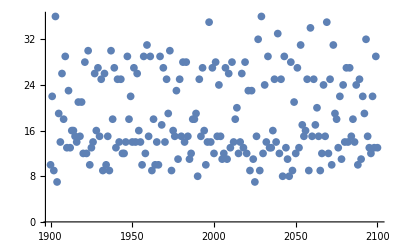

```mathematica
ListPlot[yearData]
```

## Exploration 6

### Determine how many of the first 50000 primes contain the numbers 5,4,3, and 2, in that order (but not necessarily consecutively!).

## Exploration 7

### How many Pythagorean triples (a,b,c such that a^2+b^2=c^2) are there where a, b, and c are all less than 50? 100? 500?

#### Work here:

```mathematica
MatchQ[....]
```

#### Hints (Expand cell to see)

First figure out how to create a pattern that tests whether a list of three elements is a Pythagorean triple.  (MatchQ is your friend.)
Generate all sets of triples {a,b,c} such that a<=b and a<=c so that you do not have any redundant answers.
Use Cases (or Count) to see which sets satisfy the pattern.

#### More advanced Hints

When creating your pattern, you will want to use the ? operator, pure functions, and make sure to reference parts of the list using constructions like #[[1]].
The Table command will have three variables that vary, like {a,1,100}, {b,1,100}, {c,1,100}.  How can you make sure that b is no smaller than a?  You can also restrict that c<=Sqrt[2]*b. (Why?)  
You’ll have to flatten two layers of this Table command.

#### Answer (To see if you’re on the right track before looking at the solution.)

There are 20 triples where a,b,c<=50.
There are 52 triples where a,b,c<=100.  
There are 386 triples where a,b,c<=500.

#### Partial Solution (Don’t peek!)

```mathematica
MatchQ[{3,4,5},_?(#[[1]]^2+#[[2]]^2==#[[3]]^2 &)]
```

```mathematica
possible=Flatten[Table[{a,b,c},{a,1,100},{b,a,100},{c,b,100}],2];
```

#### Faster solution

```mathematica
n=50;
possible=Flatten[Table[{a,b,c},{a,1,n},{b,a,n},{c,Floor[Sqrt[a^2+b^2]],Min[Ceiling[Sqrt[a^2+b^2]],n]}],2];
triples=Count[possible,_?(#[[1]]^2+#[[2]]^2==#[[3]]^2 &)]
```

20

### Which of these Pythagorean triples are in lowest terms?

We know that if (a,b,c) is a Pythagorean triple, then so is (ka,kb,kc).  So we should remove from the list we found above those where the greatest common divisor is greater than 1.  The command for that is GCD.  You will have to use the Apply command to make things work out well.

#### Work here:

```mathematica
GCD[3,4,5]
```

1

```mathematica
GCD[30,40,50]
```

10

#### Solution (Don’t peek!)

```mathematica
triples=Cases[possible,_?(#[[1]]^2+#[[2]]^2==#[[3]]^2 &)]
Cases[triples,_?(Apply[GCD,#]==1 &)]
```